```mathematica
Clear["Global`*"]
```

!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!

Data before calculations:

ID | direction | Pstart | Tstart | Q | Type | Pend | Tend | rhon | hs | Rspecific | Pout | Tout | L | rhostart | rhoend | Mstart | Mend
1 | {1,2} | 35. | 15. | 390000. | in | 0. | 0. | 0.7217 | 33.71 | 479.94 | 0. | 0. | 10.036 | 27.3824 | 0 | 78.1842 | 78.1842
2 | {2,3,4} | 0. | 0. | 80000. | out | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 56.896 | 0 | 0 | 0 | 0
3 | {2,5} | 0. | 0. | -1 | medium | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 14.45 | 0 | 0 | 0 | 0
4 | {5,6,9} | 0. | 0. | 20000. | out | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 44.577 | 0 | 0 | 0 | 0
5 | {5,7} | 0. | 0. | -1 | medium | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 10.22 | 0 | 0 | 0 | 0
6 | {7,10,11} | 0. | 0. | 20000. | out | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 25.486 | 0 | 0 | 0 | 0
7 | {7,8} | 0. | 0. | -1 | medium | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 11.036 | 0 | 0 | 0 | 0
8 | {14,15,8} | 34. | 12. | 250000. | in | 0. | 0. | 0.7312 | 34.8 | 473.772 | 0. | 0. | 22.072 | 27.354 | 0 | 50.7778 | 50.7778
9 | {8,12,13} | 0. | 0. | 440000. | out | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 22.072 | 0 | 0 | 0 | 0
10 | {18,17,16} | 0. | 0. | 30000. | out | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 22.072 | 0 | 0 | 0 | 0
11 | {19,18} | 33. | 13. | 200000. | in | 0. | 0. | 0.778 | 37.03 | 445.714 | 0. | 0. | 11.036 | 28.4242 | 0 | 43.2222 | 43.2222
12 | {18,20,21} | 0. | 0. | -1 | medium | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 22.072 | 0 | 0 | 0 | 0
13 | {21,23,24} | 0. | 0. | 50000. | out | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 22.072 | 0 | 0 | 0 | 0
14 | {7,25} | 0. | 0. | -1 | medium | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 24.774 | 0 | 0 | 0 | 0
15 | {25,26,27,28} | 0. | 0. | 50000. | out | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 33.108 | 0 | 0 | 0 | 0
16 | {25,29} | 0. | 0. | 150000. | out | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 11.036 | 0 | 0 | 0 | 0
17 | {21,22,8} | 0. | 0. | -1 | medium | 0. | 0. | -1 | 0. | 0. | 0. | 0. | 22.072 | 0 | 0 | 0 | 0

sumIn = 840000.

sumOut = 840000.

sumIn-sumOut = 0.

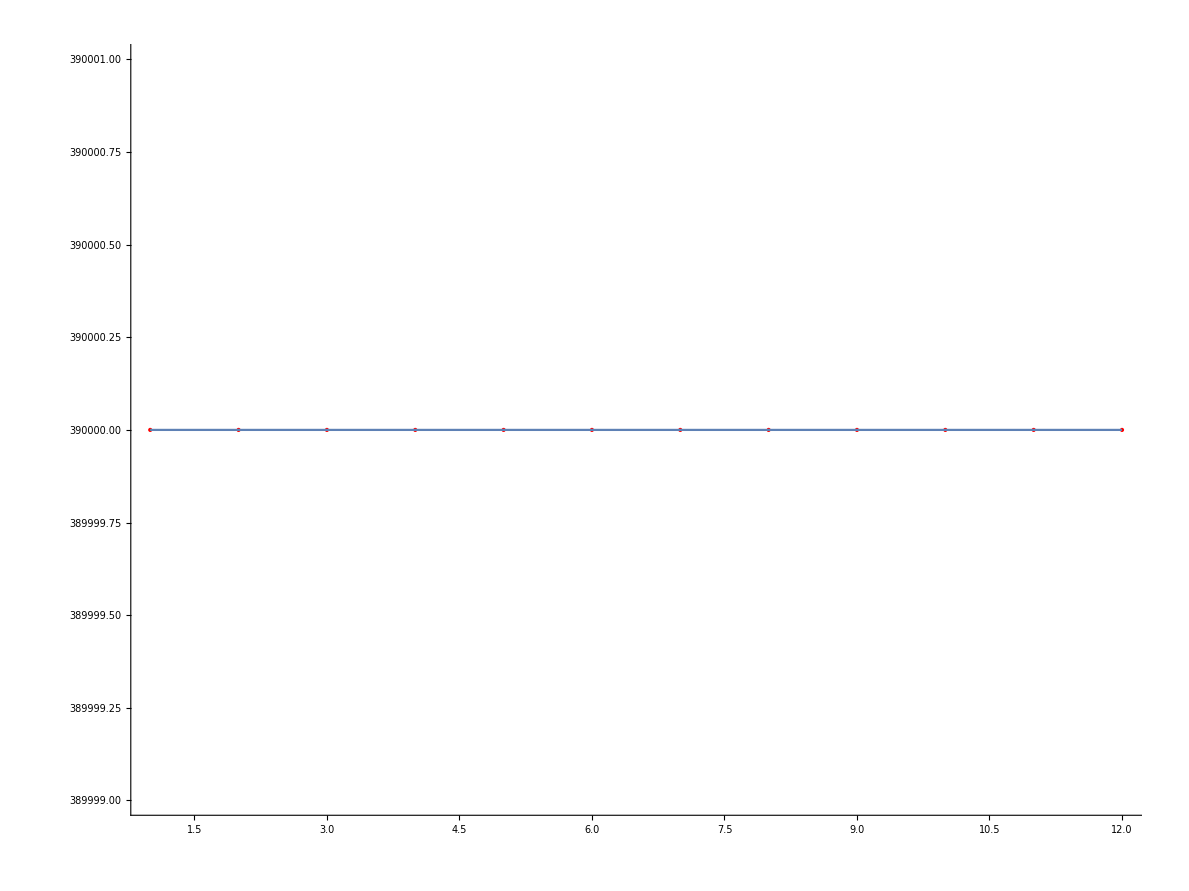

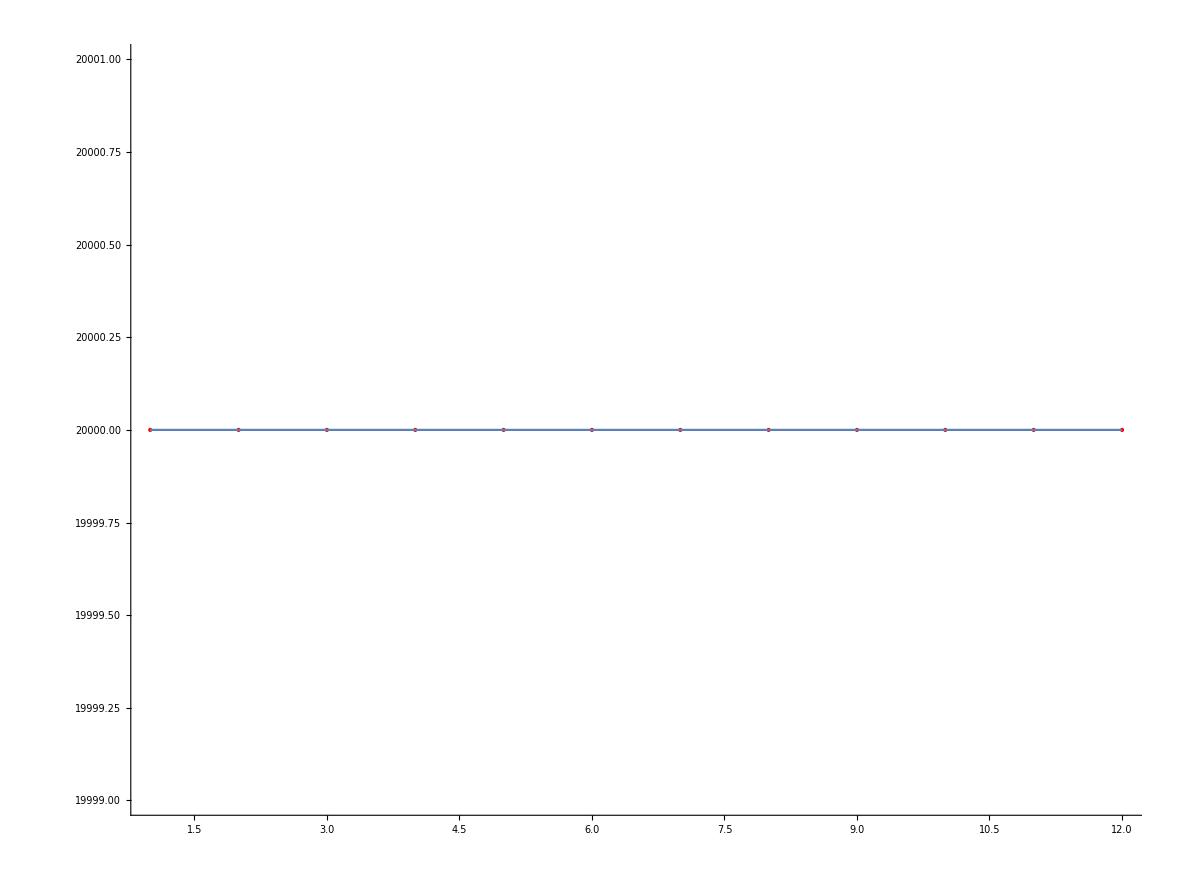

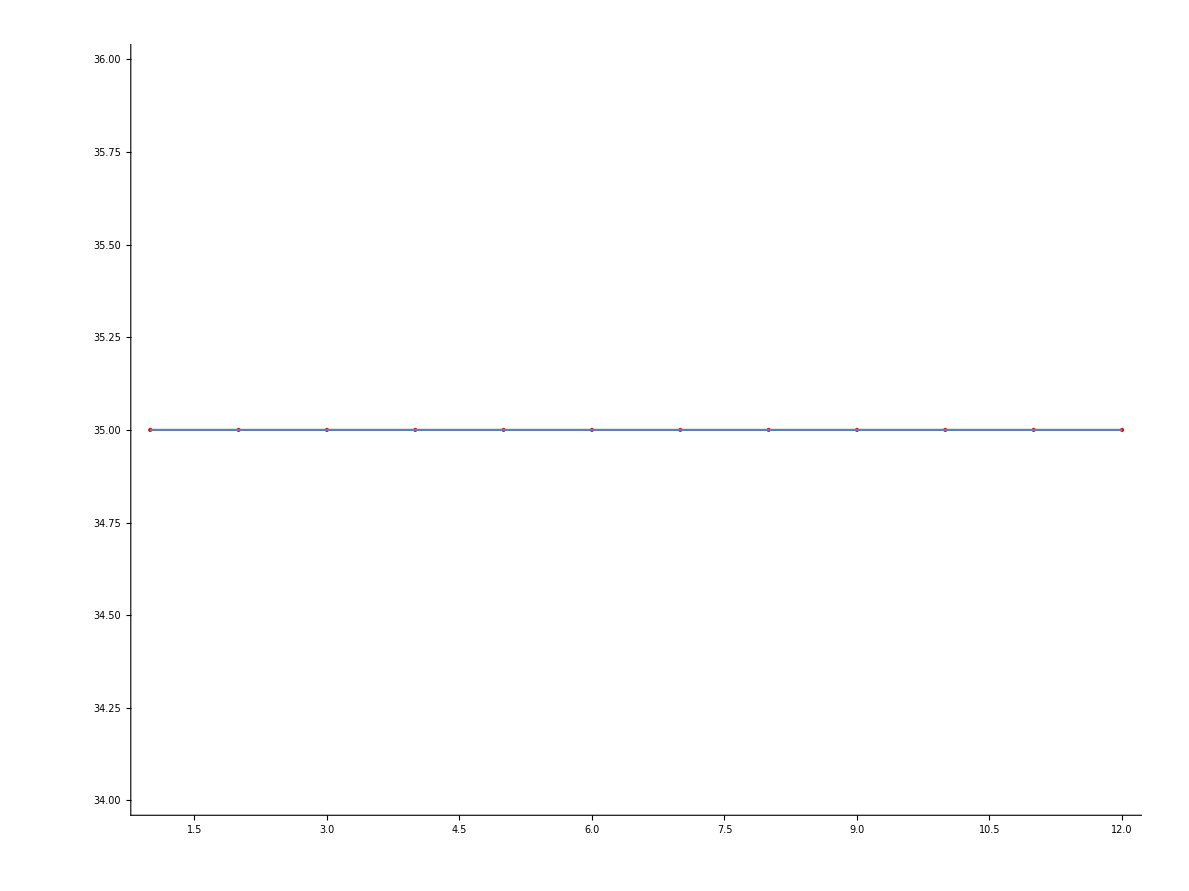

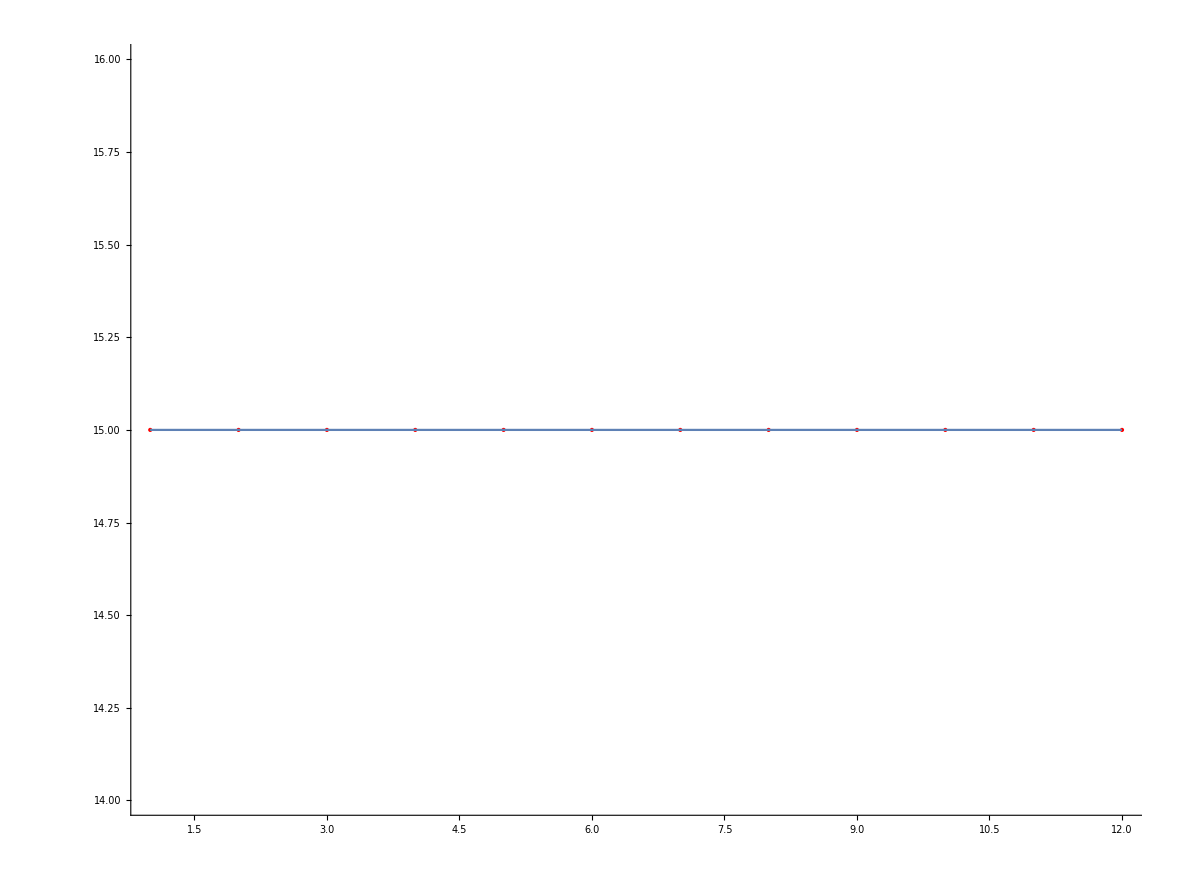

```mathematica
(*+++++*************** TOTAL WORK REGIME FOR BUKHARA-URAL *+++++***************)
(*-----------------------------GLOBAL VARIABLES-------------------------------*)
(***Import data from files***)
ksIds={{3,23620,362922}(*ks-14 a*),{29,20816,362000}(*ks-10 a*),{37,22477,362000}(*ks-10 b*),{34,27560,362000}(*ks-12*)};
kRoughness=0.03*10^(-3);(*m*)
gGrav=9.8;
(*first regime*)
(*---------------------------*)
numDirections=17;
initialDirections={};
segments=SemanticImport["/home/dinara/Documents/for_disser_31.01.2022/simone_dynamic_model_paper/data/segments-test-small.xlsx"];
sheetNames=Import["/home/dinara/Documents/for_disser_31.01.2022/simone_dynamic_model_paper/data/initial_data_total-test-regime-small-stable.xlsx","Sheets"];
numTimes=Length[sheetNames];
dataDynamic=Table[Import["/home/dinara/Documents/for_disser_31.01.2022/simone_dynamic_model_paper/data/initial_data_total-test-regime-small-stable.xlsx",{"Data",sheetNames[[k]],2;;numDirections+1}],{k,numTimes}];
For[k=1,k<=numDirections,k++,
initialDirections=Insert[initialDirections,ToExpression[StringSplit[dataDynamic[[1,k,1]],{","}]],-1];
];
(*Extract distances and diameters from segments*)
numDirectionsNonZeroQ=numDirections;
numSegments=Length[segments];
(*Construct arrays for data*)
For[k=1,k≤numSegments,k++,
start=IntegerPart[segments[[k,"Start"]]];
end=IntegerPart[segments[[k,"End"]]];
distances[start,end]=segments[[k,"L"]]*1000;
distances[end,start]=distances[start,end];
deltaH[start,end]=segments[[k,"deltaH"]];
deltaH[end,start]=-deltaH[start,end];
diameters[start,end]=segments[[k,"Diaminner"]]/1000//N;
diameters[end,start]=diameters[start,end];
kLCoef[start,end]=segments[[k,"kL"]];
kLCoef[end,start]=kLCoef[start,end];
TSoilValues[start,end]=segments[[k,"Tsoil"]];
TSoilValues[end,start]=TSoilValues[start,end];
hydraulicResistance[start,end]=0;
hydraulicResistance[end,start]=hydraulicResistance[start,end];
];
(*Add data table*)
dataInfo=Table[{"",""},{l,numDirections+1},{m,18}];
names={"ID","direction","Pstart","Tstart","Q","Type","Pend","Tend","rhon", "hs", "Rspecific", "Pout","Tout", "L","rhostart","rhoend","Mstart","Mend"};
dataInfo[[1,;;]]=names;
directions=initialDirections;
(*Set total data to map*)
For[m=1,m≤numDirections,m++,
len=Length[directions[[m]]];
totalData[m,"Pstart"]=ToExpression[dataDynamic[[1,m,2]]];
totalData[m,"P",1]=totalData[m,"Pstart"];
totalData[m,"Tstart"]=ToExpression[dataDynamic[[1,m,3]]];
totalData[m,"T",1]=totalData[m,"Tstart"];
totalData[m,"Pend"]=ToExpression[dataDynamic[[1,m,6]]];
totalData[m,"P",len]=totalData[m,"Pend"];
totalData[m,"Tend"]=ToExpression[dataDynamic[[1,m,7]]];
totalData[m,"T",len]=totalData[m,"Tend"];
totalData[m,"Type"]=ToString[dataDynamic[[1,m,5]]];
If[totalData[m,"Type"]=="medium"||totalData[m,"Type"]=="station",
totalData[m,"Q"]=-1,
totalData[m,"Q"]=ToExpression[dataDynamic[[1,m,4]]];
];
If[totalData[m,"Q"]==0,
numDirectionsNonZeroQ--;
];
totalData[m,"Rspecific"]=ToExpression[dataDynamic[[1,m,15]]];
totalData[m,"rhoend"]=0;
If[totalData[m,"Type"]!="in",
totalData[m,"rhostart"]=0;
totalData[m,"rhon"]=-1;
totalData[m,"Mstart"]=0;
totalData[m,"Mend"]=0,
totalData[m,"rhon"]=ToExpression[dataDynamic[[1,m,10]]];
totalData[m,"Mstart"]=totalData[m,"Q"]*totalData[m,"rhon"]/3600//N;
totalData[m,"Mend"]=totalData[m,"Mstart"];
totalData[m,"rhostart"]=calculateZ[totalData[m,"rhon"],kg2pa[totalData[m,"Pstart"]]*10^(-6),totalData[m,"Tstart"]+273.15,totalData[m,"Rspecific"]];
totalData[m,"rhostart"]=kg2pa[totalData[m,"Pstart"]]/(totalData[m,"rhostart"]*totalData[m,"Rspecific"]*(totalData[m,"Tstart"]+273.15));
];
totalData[m,"Pout"]=ToExpression[dataDynamic[[1,m,8]]];
totalData[m,"Tout"]=ToExpression[dataDynamic[[1,m,9]]];
totalData[m,"hs"]=ToExpression[dataDynamic[[1,m,13]]];
totalData[m,"Mmolar"]=ToExpression[dataDynamic[[1,m,14]]];
numIndexes=Length[directions[[m]]]-1;
indexes=Table[{0,0},{ll,numIndexes}];
For[k=1,k<=Length[indexes],k++,
indexes[[k]]={directions[[m,k]],directions[[m,k+1]]};
];
totalData[m,"L"]=Sum[distances[IntegerPart[ll[[1]]],IntegerPart[ll[[2]]]]/1000//N,{ll,indexes}];
dataInfo[[m+1,;;]]={m,directions[[m]],totalData[m,"Pstart"],totalData[m,"Tstart"],
totalData[m,"Q"],totalData[m,"Type"],totalData[m,"Pend"],totalData[m,"Tend"],
totalData[m,"rhon"],totalData[m,"hs"],totalData[m,"Rspecific"],totalData[m,"Pout"],totalData[m,"Tout"],totalData[m,"L"],totalData[m,"rhostart"],totalData[m,"rhoend"],totalData[m,"Mstart"],totalData[m,"Mend"]};
];
Print["!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!"];
Print["Data before calculations:"];
Grid[dataInfo,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightCyan,None},{LightGreen,None}}]
(*Check Kirchhoff's first law*)
sumIn=0;
sumOut=0;
For[s=1,s<=numDirections,s++,
If[totalData[s,"Type"]=="in",
sumIn=sumIn+totalData[s,"Q"];
];
If[totalData[s,"Type"]=="out",
sumOut=sumOut+totalData[s,"Q"];
];
];
Print["sumIn = ", sumIn];
Print["sumOut = ", sumOut];
Print["sumIn-sumOut = ",sumIn-sumOut];
(*Find common vertices in last point and common start point for all directions*)
commonTotalLastVertices={};(*see image from explanation/images/communication_types/commonLastVertices.jpeg*)
commonTotalStartPoint={};(*see image from explanation/images/communication_types/commonStartPoint.jpeg*)
commonTotalStartVertices={};(*see image from explanation/images/communication_types/commonStartVertices.jpeg*)
commonTotalStartPointInverse={};(*see image from explanation/images/communication_types/commonTotalStartPointInverse.jpeg*)
constructCommunicationTypes[];
calculatedDirections={};
directionIndexes=Table[k,{k,numDirections}];
checkeDirections={};
crossingValues={2,5,7,25,8,18,21};
numCrossings=Length[crossingValues];
For[k=1,k<=numCrossings,k++,
crossings[k,"value"]=0;
crossings[k,"out"]={};
crossings[k,"in"]={};
];
atmP=0.099991;atmT=-21;
vCoef=0.473;
tau=0.01;
lambdaCoef=7;
SMatrix=Table[0,{i,numCrossings},{k,numCrossings}];
RVector=Table[0,{i,numCrossings}];
iterationCount=2000;
(*construct splines*)
inDirections={};outDirections={};
For[m=1,m<=numDirections,m++,
Which[totalData[m,"Type"]=="in",
inDirections=Insert[inDirections,m,-1],
totalData[m,"Type"]=="out",
outDirections=Insert[outDirections,m,-1];
];
];
QIns=Table[dataDynamic[[l,inDirections[[k]],4]],{k,Length[inDirections]},{l,numTimes}];
QOuts=Table[dataDynamic[[l,outDirections[[k]],4]],{k,Length[outDirections]},{l,numTimes}];
pIns=Table[dataDynamic[[l,inDirections[[k]],2]],{k,Length[inDirections]},{l,numTimes}];
TIns=Table[dataDynamic[[l,inDirections[[k]],3]],{k,Length[inDirections]},{l,numTimes}];
ptsQIns=Table[{l,QIns[[k,l]]},{k,Length[QIns]},{l,numTimes}];
ptsQOuts=Table[{l,QOuts[[k,l]]},{k,Length[QOuts]},{l,numTimes}];
ptsPIns=Table[{l,pIns[[k,l]]},{k,Length[pIns]},{l,numTimes}];
ptsTIns=Table[{l,TIns[[k,l]]},{k,Length[TIns]},{l,numTimes}];
splineQIns=Table[BSplineFunction[ptsQIns[[k]]],{k,Length[QIns]}];
splineQOuts=Table[BSplineFunction[ptsQOuts[[k]]],{k,Length[QOuts]}];
splinePIns=Table[BSplineFunction[ptsPIns[[k]]],{k,Length[pIns]}];
splineTIns=Table[BSplineFunction[ptsTIns[[k]]],{k,Length[TIns]}];
(*show graphics for first splines*)
Show[Graphics[{Red,Point[ptsQIns[[1]]],Green,Line[ptsQIns[[1]]]},Axes->True],ParametricPlot[splineQIns[[1]][t],{t,0,1}]]
Show[Graphics[{Red,Point[ptsQOuts[[3]]],Green,Line[ptsQOuts[[3]]]},Axes->True],ParametricPlot[splineQOuts[[3]][t],{t,0,1}]]
Show[Graphics[{Red,Point[ptsPIns[[1]]],Green,Line[ptsPIns[[1]]]},Axes->True],ParametricPlot[splinePIns[[1]][t],{t,0,1}]]
Show[Graphics[{Red,Point[ptsTIns[[1]]],Green,Line[ptsTIns[[1]]]},Axes->True],ParametricPlot[splineTIns[[1]][t],{t,0,1}]]
```

```mathematica
(*check circulation for directions*)
For[id=1,id<=numDirections,id++,
ancestors=commonTotalStartPointInverse[[id]];
If[Length[ancestors]>0,
If[checkCirculation[ancestors,id],
Print["============================="];
Print["============================="];
Print["Detected circulation"];
Break[];
];
];
(*clear array for checked directions*)
checkeDirections={};
];
```